```mathematica
Clear["*"];
```

```mathematica
$DisplayFunction=Identity;
```

```mathematica
Kx=0;Ky=0;Kz=0;Kd={1000000,1000000,1000000};
```

```mathematica
ω0=2 Pi/360000;
```

```mathematica
ωinit={.3,.5,.4}; qinit={.5,.5,.5,.5};
```

```mathematica
Bx={0.06073800000000001,0.029804,-0.0005790600000000001,-0.030350000000000002,-0.059532,-0.088197,-0.11644000000000002,-0.14433,-0.17190000000000003,-0.19913000000000003,-0.22592,-0.25209000000000004,-0.27740000000000004,-0.30157,-0.32424000000000003,-0.34505,-0.36364,-0.37967,-0.39287000000000005,-0.40307000000000004,-0.41021,-0.41439000000000004,-0.41584000000000004,-0.41493,-0.41209,-0.40782,-0.40257,-0.39669,-0.39044,-0.3839,-0.377,-0.36955000000000005,-0.36129,-0.35191,-0.34111,-0.32866,-0.31437000000000004,-0.29813,-0.27989,-0.25969000000000003,-0.23761000000000002,-0.2138,-0.1885,-0.16203,-0.13481,-0.10731,-0.08009600000000001,-0.053726,-0.028731,-0.0055567,0.015477000000000001,0.0342,0.050598000000000004,0.064791,0.077007,0.08753500000000002,0.096696,0.10482000000000001,0.11221000000000002,0.11921,0.12613000000000002,0.13332,0.14117,0.15005000000000002,0.16034,0.17235,0.18629,0.20225,0.22014,0.2397,0.26055,0.28218000000000004,0.30406,0.32564000000000004,0.34640000000000004,0.36593000000000003,0.38386000000000003,0.39993,0.41390000000000005,0.42561000000000004,0.43492,0.44172000000000006,0.44589999999999996,0.44744000000000006,0.44632,0.44257,0.43625,0.42743000000000003,0.41618000000000005,0.40253,0.38650000000000007,0.36809000000000003,0.34729000000000004,0.32412,0.29864,0.27099,0.24136000000000002,0.21004,0.17731,0.14347000000000001,0.10881000000000002}
```

{0.060738,0.029804,-0.00057906,-0.03035,-0.059532,-0.088197,-0.11644,-0.14433,-0.1719,-0.19913,-0.22592,-0.25209,-0.2774,-0.30157,-0.32424,-0.34505,-0.36364,-0.37967,-0.39287,-0.40307,-0.41021,-0.41439,-0.41584,-0.41493,-0.41209,-0.40782,-0.40257,-0.39669,-0.39044,-0.3839,-0.377,-0.36955,-0.36129,-0.35191,-0.34111,-0.32866,-0.31437,-0.29813,-0.27989,-0.25969,-0.23761,-0.2138,-0.1885,-0.16203,-0.13481,-0.10731,-0.080096,-0.053726,-0.028731,-0.0055567,0.015477,0.0342,0.050598,0.064791,0.077007,0.087535,0.096696,0.10482,0.11221,0.11921,0.12613,0.13332,0.14117,0.15005,0.16034,0.17235,0.18629,0.20225,0.22014,0.2397,0.26055,0.28218,0.30406,0.32564,0.3464,0.36593,0.38386,0.39993,0.4139,0.42561,0.43492,0.44172,0.4459,0.44744,0.44632,0.44257,0.43625,0.42743,0.41618,0.40253,0.3865,0.36809,0.34729,0.32412,0.29864,0.27099,0.24136,0.21004,0.17731,0.14347,0.10881}

```mathematica
By={-0.24416000000000004,-0.24391,-0.24251999999999999,-0.24022000000000002,-0.23715000000000003,-0.23344,-0.22911000000000004,-0.22413,-0.21841,-0.21183000000000002,-0.20424000000000003,-0.19552000000000003,-0.18555,-0.17427,-0.16166000000000003,-0.14778,-0.13279000000000002,-0.11691000000000001,-0.10049999999999999,-0.083988,-0.067936,-0.053023,-0.040147,-0.030621000000000002,-0.026404,-0.029241000000000003,-0.037505000000000004,-0.047085,-0.056273000000000004,-0.065197,-0.074229,-0.08363899999999999,-0.09357,-0.10405,-0.11502,-0.12632000000000002,-0.13774,-0.14906,-0.16001,-0.17034000000000002,-0.17977,-0.18804,-0.19486000000000003,-0.19999,-0.20318999999999998,-0.20432000000000003,-0.20333,-0.20026000000000002,-0.19533,-0.18883000000000003,-0.18117000000000003,-0.17278000000000002,-0.16413,-0.15561000000000003,-0.14757,-0.14028000000000002,-0.13391,-0.12860000000000002,-0.12441,-0.12141,-0.11961,-0.119,-0.11954000000000001,-0.12108000000000002,-0.12341,-0.12619,-0.12902,-0.13140000000000002,-0.13277000000000003,-0.13257000000000002,-0.13021000000000002,-0.12499,-0.11591000000000001,-0.10123,-0.07792600000000001,-0.043405,-0.0047219,0.021259,0.029801,0.026841,0.017621,0.0049613,-0.0096904,-0.025529000000000003,-0.042055999999999996,-0.05894,-0.075952,-0.092936,-0.10979000000000001,-0.12642,-0.14277,-0.15874,-0.17419,-0.18896000000000002,-0.20283000000000004,-0.21559,-0.22704000000000002,-0.23702,-0.24542000000000003,-0.25219,-0.25733}
```

{-0.24416,-0.24391,-0.24252,-0.24022,-0.23715,-0.23344,-0.22911,-0.22413,-0.21841,-0.21183,-0.20424,-0.19552,-0.18555,-0.17427,-0.16166,-0.14778,-0.13279,-0.11691,-0.1005,-0.083988,-0.067936,-0.053023,-0.040147,-0.030621,-0.026404,-0.029241,-0.037505,-0.047085,-0.056273,-0.065197,-0.074229,-0.083639,-0.09357,-0.10405,-0.11502,-0.12632,-0.13774,-0.14906,-0.16001,-0.17034,-0.17977,-0.18804,-0.19486,-0.19999,-0.20319,-0.20432,-0.20333,-0.20026,-0.19533,-0.18883,-0.18117,-0.17278,-0.16413,-0.15561,-0.14757,-0.14028,-0.13391,-0.1286,-0.12441,-0.12141,-0.11961,-0.119,-0.11954,-0.12108,-0.12341,-0.12619,-0.12902,-0.1314,-0.13277,-0.13257,-0.13021,-0.12499,-0.11591,-0.10123,-0.077926,-0.043405,-0.0047219,0.021259,0.029801,0.026841,0.017621,0.0049613,-0.0096904,-0.025529,-0.042056,-0.05894,-0.075952,-0.092936,-0.10979,-0.12642,-0.14277,-0.15874,-0.17419,-0.18896,-0.20283,-0.21559,-0.22704,-0.23702,-0.24542,-0.25219,-0.25733}

```mathematica
Bz={0.029178000000000003,0.026264,0.023045,0.019519,0.015709,0.011663,0.0074551999999999995,0.0031835,-0.001038,-0.0050853,-0.008833,-0.012162,-0.014965,-0.017152,-0.018648,-0.019396,-0.019354,-0.018497,-0.016808,-0.014286000000000002,-0.010939,-0.0067862,-0.0018846000000000002,0.0035556999999999997,0.0087159,0.011371000000000001,0.0093246,0.0041183,-0.0014878,-0.0063983,-0.010473,-0.013814,-0.016556,-0.018836,-0.020781,-0.022514,-0.024146,-0.025779999999999997,-0.027505,-0.029396000000000002,-0.031506,-0.033862,-0.036461,-0.039265,-0.042197,-0.045148,-0.047982,-0.050551000000000006,-0.052707,-0.05432000000000001,-0.05529200000000001,-0.055566000000000004,-0.055128,-0.054007,-0.052263000000000004,-0.049970999999999995,-0.047214,-0.044061,-0.040561,-0.036738,-0.03259,-0.028096000000000003,-0.023222,-0.017931,-0.012191,-0.005975500000000001,0.0007316200000000001,0.0079494,0.015714,0.024109,0.033303,0.043605,0.055499,0.069468,0.08491,0.09680899999999999,0.09543,0.081161,0.06503199999999999,0.052567,0.043968,0.038217,0.034390000000000004,0.031823000000000004,0.030063,0.028804,0.027842,0.027042000000000004,0.026317,0.025611000000000002,0.02489,0.024128,0.023307,0.022407,0.021407,0.020280999999999997,0.018998,0.017523,0.015822,0.013864000000000001,0.01163}
```

{0.029178,0.026264,0.023045,0.019519,0.015709,0.011663,0.0074552,0.0031835,-0.001038,-0.0050853,-0.008833,-0.012162,-0.014965,-0.017152,-0.018648,-0.019396,-0.019354,-0.018497,-0.016808,-0.014286,-0.010939,-0.0067862,-0.0018846,0.0035557,0.0087159,0.011371,0.0093246,0.0041183,-0.0014878,-0.0063983,-0.010473,-0.013814,-0.016556,-0.018836,-0.020781,-0.022514,-0.024146,-0.02578,-0.027505,-0.029396,-0.031506,-0.033862,-0.036461,-0.039265,-0.042197,-0.045148,-0.047982,-0.050551,-0.052707,-0.05432,-0.055292,-0.055566,-0.055128,-0.054007,-0.052263,-0.049971,-0.047214,-0.044061,-0.040561,-0.036738,-0.03259,-0.028096,-0.023222,-0.017931,-0.012191,-0.0059755,0.00073162,0.0079494,0.015714,0.024109,0.033303,0.043605,0.055499,0.069468,0.08491,0.096809,0.09543,0.081161,0.065032,0.052567,0.043968,0.038217,0.03439,0.031823,0.030063,0.028804,0.027842,0.027042,0.026317,0.025611,0.02489,0.024128,0.023307,0.022407,0.021407,0.020281,0.018998,0.017523,0.015822,0.013864,0.01163}

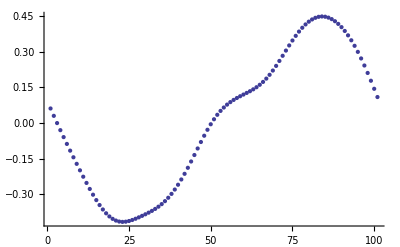

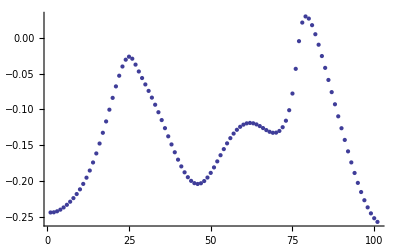

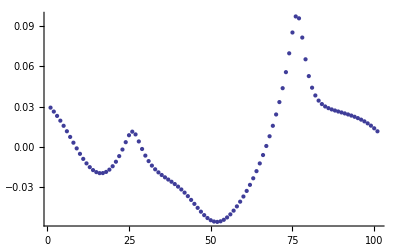

```mathematica
ListPlot[Bx]
ListPlot[By]
ListPlot[Bz]
```

```mathematica
fBx=Interpolation[Table[{i,Bx[[i]]},{i,1,Dimensions[Bx][[1]]}]]
fBy=Interpolation[Table[{i,By[[i]]},{i,1,Dimensions[Bx][[1]]}]]
fBz=Interpolation[Table[{i,Bz[[i]]},{i,1,Dimensions[Bx][[1]]}]]
```

InterpolatingFunction[{{1.,101.}},<>]

InterpolatingFunction[{{1.,101.}},<>]

InterpolatingFunction[{{1.,101.}},<>]

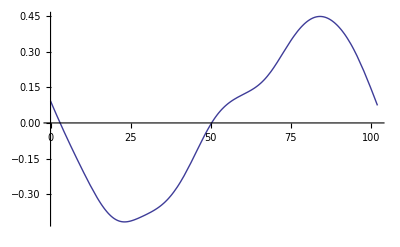

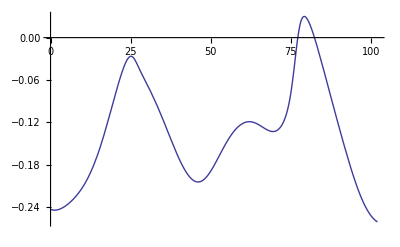

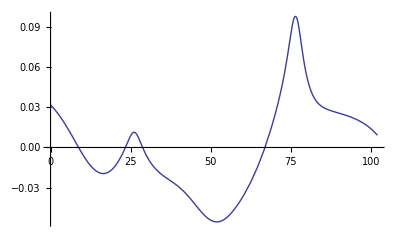

```mathematica
Plot[fBx[t],{t,0,102}]
Plot[fBy[t],{t,0,102}]
Plot[fBz[t],{t,0,102}]
```

```mathematica
fBx[100]
```

0.14347

```mathematica
Bo[t_]:= (10^-3)*{fBx[t],fBy[t],fBz[t]};
```

```mathematica
Bdoto[t_]:=(10^-3)*{fBx'[t],fBy'[t],fBz'[t]};
```

```mathematica
Ix=1;Iy=2;Iz=3;
```

```mathematica
n=3.2;
```

```mathematica
P[v_]:=0.5*Table[{{0, v[[3]],-v[[2]], v[[1]]},{-v[[3]], 0, v[[1]], v[[2]]},{v[[2]],-v[[1]], 0, v[[3]]},{-v[[1]],-v[[2]],-v[[3]], 0}}]
```

```mathematica
skewsym[v_]:=Table[{{0, v[[3]],-v[[2]]},{-v[[3]], 0, v[[1]]},{v[[2]],-v[[1]], 0}}]
```

```mathematica
Isat=Table[{{Ix,0,0},{0,Iy,0},{0,0,Iz}}];
```

```mathematica
σ1=(Iy-Iz)/Ix; σ2=(Iz-Ix)/Iy;σ3=(Ix-Iy)/Iz;
```

```mathematica
quaternioninverse[q_]:={-q[[1]],-q[[2]],-q[[3]],q[[4]]}
```

```mathematica
quaternionmultiply[q1_,q2_]:={q2[[4]] q1[[1]] +q2[[1]] q1[[4]]-q2[[2]] q1[[3]]+q2[[3]] q1[[2]],q2[[4]] q1[[2]]+q2[[1]] q1[[3]]+q2[[2]] q1[[4]]-q2[[3]] q1[[1]],q2[[4]] q1[[3]]-q2[[1]] q1[[2]]+q2[[2]] q1[[1]]+q2[[3]] q1[[4]],q1[[4]] q2[[4]]-q1[[1]] q2[[1]]-q1[[2]] q2[[2]]-q1[[3]] q2[[3]]}
```

```mathematica
quaternionrotate[q_,v_]:={{1-2q[[2]]^2-2q[[3]]^2,2(q[[1]] q[[2]]+q[[4]] q[[3]]),2(q[[1]] q[[3]]-q[[4]] q[[2]])},{2(q[[1]] q[[2]]-q[[4]] q[[3]]),1-2q[[1]]^2-2q[[3]]^2,2(q[[2]] q[[3]]+q[[4]] q[[1]])},{2(q[[1]] q[[3]]+q[[4]] q[[2]]),2(q[[2]] q[[3]]-q[[4]] q[[1]]),1-2q[[1]]^2-2q[[2]]^2}}.v
```

```mathematica
τc[q_,qreq_,ω_,t_]:=(
qe={{qreq[[4]],qreq[[3]],-qreq[[2]],qreq[[1]]},{-qreq[[3]],qreq[[4]],qreq[[1]],qreq[[2]]},{qreq[[2]],-qreq[[1]],qreq[[4]],qreq[[3]]},{-qreq[[1]],-qreq[[2]],-qreq[[3]],qreq[[4]]}}.quaternioninverse[q];
Bb=quaternionrotate[q,Bo[t]];
Bdotb=quaternionrotate[q,Bo[t]];
Table[2 Kx qe[[i]] qe[[4]]+Kd[[i]] Cross[(Cross[ω,Bb]-Bdotb),Bb][[i]],{i,1,3}])
```

```mathematica
QuaternionDerivative[x_,ω_]:=P[ω].x
```

```mathematica
AngVelDerivative[ω_,τ_]:=Inverse[Isat].τ-{σ1 ω[[2]] ω[[3]],σ2 ω[[3]] ω[[1]],σ3 ω[[1]] ω[[2]]}
```

```mathematica
eqs3={Table[y[i]'[x]==QuaternionDerivative[Table[y[j][x],{j,1,4}],Table[y[i][x],{i,5,7}]-quaternionrotate[Table[y[i][x],{i,1,4}],{0,ω0,0}]][[i]],{i,1,4}],Table[y[i][0]== qinit[[i]],{i,1,4}],
Table[y[i]'[x]==AngVelDerivative[Table[y[j][x],{j,5,7}],τc[Table[y[i][x],{i,1,4}],{0,0,0,1},Table[y[i][x],{i,5,7}],x]][[i-4]],{i,5,7}],Table[y[i][0]== ωinit[[i-4]],{i,5,7}]};
```

```mathematica
Needs["DifferentialEquations`NDsol2veProblems`"];
Needs["DifferentialEquations`NDsol2veUtilities`"];
Needs["FunctionApproximations`"];
```

```mathematica
sol3=NDSolve[eqs3,Table[y[i],{i,1,7}],{x,0,10^n}]
```

{{y[1]→InterpolatingFunction[{{0.,1584.89}},<>],y[2]→InterpolatingFunction[{{0.,1584.89}},<>],y[3]→InterpolatingFunction[{{0.,1584.89}},<>],y[4]→InterpolatingFunction[{{0.,1584.89}},<>],y[5]→InterpolatingFunction[{{0.,1584.89}},<>],y[6]→InterpolatingFunction[{{0.,1584.89}},<>],y[7]→InterpolatingFunction[{{0.,1584.89}},<>]}}

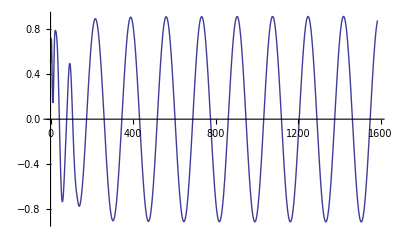

```mathematica
Plot[Evaluate[y[1][x]/.sol3,{x,0,10^n}],PlotRange->Full]
```

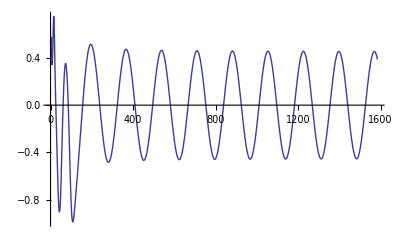

```mathematica
Plot[Evaluate[y[2][x]/.sol3,{x,0,10^n}],PlotRange->Full]
```

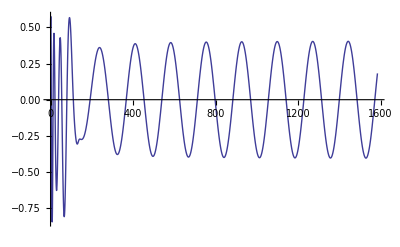

```mathematica
Plot[Evaluate[y[3][x]/.sol3,{x,0,10^n}],PlotRange->Full]
```

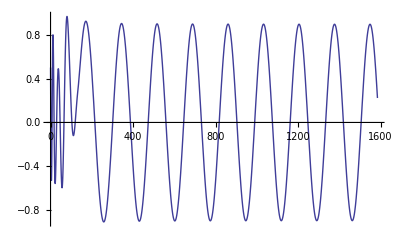

```mathematica
Plot[Evaluate[y[4][x]/.sol3,{x,0,10^n}],PlotRange->Full]
```

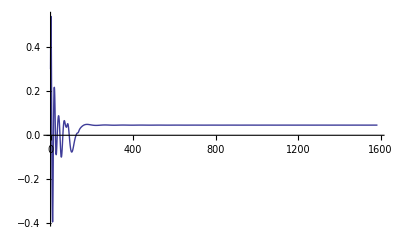

```mathematica
Plot[Evaluate[y[5][x]/.sol3,{x,0,10^n}],PlotRange->{Full,All}]
```

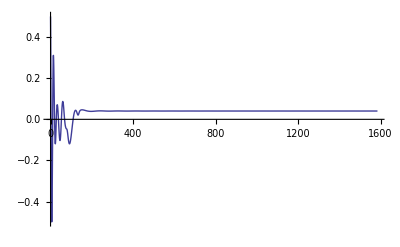

```mathematica
Plot[Evaluate[y[6][x]/.sol3,{x,0,10^n}],PlotRange->{Full,All}]
```

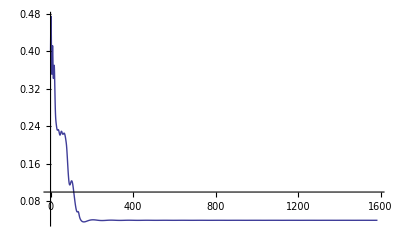

```mathematica
Plot[Evaluate[y[7][x]/.sol3,{x,0,10^n}],PlotRange->{Full,All}]
```